```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
(*Calcula os pontos e os pesos da regra de integração *)
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order+1,-1,1]];
pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
(*dado a ordem polinomial gera as funções de forma definidas no elemento mestre -  lineares *)
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
(*list=ListPoli[npoints];
Table[list[[i]],{i,Length[list],1,-1}]*)
ListPoli[npoints]
]
```

```mathematica
(*dado a ordem polinomial gera as funções de forma definidas no elemento mestre -  quadrilátero *)
GeneratePsis[order_]:=Block[{sz,i,j,w,psis,temp,xi,eta},
sz=(2+order-1)(2+order-1);
psis=Table[0,{sz}];
temp=1;
For[i=1,i≤ 1+order,i++,
For[j=1,j≤ 1+order,j++,
psis[[temp]]=(ComputeShape[order,xi][[j]]ComputeShape[order,eta][[i]])*(1);
temp++;
];
];
psis
];
```

```mathematica
Forcing[x_,y_]:=Block[{},
0
]
```

```mathematica
(*Calcula a contribuição da equação diferencial do problema de elasticidade (ek e ef) em cada ponto de integração *)
ContributeElastic[data_,weight_,order_]:=Block[{C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},
nnodes=4 order ;
{psi,GradPsi,Jac,x,y}=data;
(*Print["Jac= ",Jac//MatrixForm];
Print["GradPsi= ",GradPsi//MatrixForm];*)
InvJac=Inverse[Jac];

DetJ=Det[Jac];
(*Print["DetJac = ",DetJ];*)
(*Print["InvJac= ",InvJac//MatrixForm];*)
(*GradPhi=Table[InvJac .GradPsi[[i]],{i,1,Length[GradPsi]}];*)
(*Print["InvJac =",InvJac];
Print["Transpose[GradPsi] =",Transpose[GradPsi]];*)
GradPhi=InvJac.Transpose[GradPsi];
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
(*Print["C = ",C//MatrixForm];*)
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
fu=-1;
For[i=1,i≤ nnodes,i++,

(*Print["x = ",x];*)
ef[[2i+fu]] +=(Forcing[x,y] psi[[i]])*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]])*wpLocal;
(*ef[[(2*i+fu)]]+=
ef[[(2*i+fu)]]+=
ef[[(2*i+1+fu)]]+=
ef[[(2*i+1+fu)]]+=*)
For[j=1,j≤ nnodes,j++,
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  1.3;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal 1.3;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal 1.3;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal 1.3;
];
];
(*Print["ek =",ek//MatrixForm];*)
{ek,ef}
]
```

```mathematica
(*Cria um grid de quadriláteros com nós ordenados no sentido anti-horário*)
CreateRectangularMesh[a_,b_,nx_,ny_,order_]:=Block[{cols,rows,coords,i,j,deltax,deltay,co1,co2,co3,co4,co5,co6,co7,co8,elvec,xstart,ystart,temp},

cols=(nx+2);
rows=(ny+2);
coords=Table[0,{rows},{cols}];

deltax=(b[[1]]-a[[1]])/(nx+1);
deltay=(b[[2]]-a[[2]])/(ny+1);
xstart=a[[1]];
ystart=a[[2]];
temp={0,0};

For[i=1,i≤ rows,i++,
For[j=1,j≤cols,j++,
coords[[i,j]]={xstart,ystart};
xstart+=deltax;
];
ystart+=deltay;
xstart=a[[1]];
];

elvec={};
For[i=1,i<rows,i++,
For[j=1,j<cols,j++,
If[order==1,
co1=coords[[i,j]];
co2=coords[[i,j+1]];
co3=coords[[i+1,j]];
co4=coords[[i+1,j+1]];
AppendTo[elvec,{co1,co2,co4 ,co3}];
];

If[order==2,
co1=coords[[i,j]];
co2=coords[[i,j+1]];
co3=coords[[i+1,j]];
co4=coords[[i+1,j+1]];

co5=co1;
co5[[1]]+=deltax/2;
co6=co2;
co6[[2]]+=deltay/2;
co7=co4;
co7[[1]]-=deltax/2;
co8=co3;
co8[[2]]-=deltay/2;
AppendTo[elvec,{co1,co2,co4 ,co3,co5,co6,co7,co8}];
];

];
];
elvec
]
```

```mathematica
8/3.
```

2.66667

```mathematica
allcoords[[1]]//N
```

Part::partd: Part specification allcoords⟦1⟧ is longer than depth of object.

allcoords⟦1⟧

```mathematica
8/3.
```

2.66667

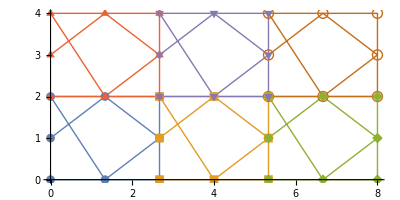

```mathematica
allcoords=CreateRectangularMesh[{0,0},{8,4},2,1,2];
undefplot=ListLinePlot[Sort[allcoords,#1[[2]]<#2[[2]]&],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}]
```

```mathematica
allcoords
```

{{{0,0},{8/3,0},{8/3,2},{0,2},{4/3,0},{8/3,1},{4/3,2},{0,1}},{{8/3,0},{16/3,0},{16/3,2},{8/3,2},{4,0},{16/3,1},{4,2},{8/3,1}},{{16/3,0},{8,0},{8,2},{16/3,2},{20/3,0},{8,1},{20/3,2},{16/3,1}},{{0,2},{8/3,2},{8/3,4},{0,4},{4/3,2},{8/3,3},{4/3,4},{0,3}},{{8/3,2},{16/3,2},{16/3,4},{8/3,4},{4,2},{16/3,3},{4,4},{8/3,3}},{{16/3,2},{8,2},{8,4},{16/3,4},{20/3,2},{8,3},{20/3,4},{16/3,3}}}

```mathematica
(*dado uma matriz de coordenadas e elementos, retorna as coordenadas globais ordenadas de acordo com a topologia global*)
ComputeNNodes[RectangularMesh_]:=Block[{allnodes,i,j,alreadcomputednodes,node,newnode,nnodes,y0,nn,firstrow,resto},
allnodes=Flatten[RectangularMesh,1]//N;
y0=allnodes[[1,2]];
(*Print[allnodes];*)
alreadcomputednodes={};
For[i=1,i≤Length[allnodes],i++,
node=allnodes[[i]];
For[j=1+i,j<=Length[allnodes],j++,
If[node==allnodes[[j]], AppendTo[alreadcomputednodes,node]];
];
];
(*Print[alreadcomputednodes];*)
newnode=allnodes;
For[i=1,i<=Length[alreadcomputednodes],i++,
newnode=DeleteCases[newnode,alreadcomputednodes[[i]]];
AppendTo[newnode,alreadcomputednodes[[i]]];

];
nn=newnode;
firstrow={};
resto={};
For[i=1,i≤Length[nn],i++,
If[nn[[i,2]]==y0,
AppendTo[firstrow,nn[[i]]];
,
AppendTo[resto,nn[[i]]];
];
firstrow=SortBy[firstrow,Last];
resto=SortBy[resto,Last];
resto=Sort[resto,#1[[2]]<#2[[2]]&];
];
PrependTo[resto,firstrow];
ArrayReshape[resto,{Length[nn],2}]
];
```

```mathematica
allcoords
```

{{{0,0},{8/3,0},{8/3,2},{0,2},{4/3,0},{8/3,1},{4/3,2},{0,1}},{{8/3,0},{16/3,0},{16/3,2},{8/3,2},{4,0},{16/3,1},{4,2},{8/3,1}},{{16/3,0},{8,0},{8,2},{16/3,2},{20/3,0},{8,1},{20/3,2},{16/3,1}},{{0,2},{8/3,2},{8/3,4},{0,4},{4/3,2},{8/3,3},{4/3,4},{0,3}},{{8/3,2},{16/3,2},{16/3,4},{8/3,4},{4,2},{16/3,3},{4,4},{8/3,3}},{{16/3,2},{8,2},{8,4},{16/3,4},{20/3,2},{8,3},{20/3,4},{16/3,3}}}

```mathematica
(*Dado uma matriz de coordenadas e elementos retorna a topologia dos elementos *)
ComputeTopol[allnodes_,order_]:=Block[{s,ss,i,j,k,topol,topolvec,topolgeral,sz=2 order},
topolvec={};
s=allnodes//N;
ss=ComputeNNodes[s]//N;
Print["Length[s] = ",Length[s]];
topolgeral={};
For[i=1,i≤Length[s],i++,

topol=Table[0,{sz}];
For[j=1,j≤sz,j++,
For[k=1,k≤Length[ss],k++,
If[s[[i,j]]==ss[[k]],
topol[[j]]=k;
AppendTo[topolgeral,k];
];
];

];
AppendTo[topolvec,topol];

];
topolvec
];
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
ApplyNodeBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,

(*Newman - Specified Load*)
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];

];
{kglob,fglob}
]
```

```mathematica
(*dado duas coordenas e a ordem de interpolação divide a linha no número de dós necessários*)
ComputeNewLinearNodes[order_,coords_]:=Block[{xa,xb,newcoords},
xa=coords[[1]];
xb=coords[[2]];
newcoords=Table[xa+(1-i)(xa-xb)/order,{i,1,order+1}];
newcoords
]
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLine[EK_,EF_,fx_,order_,nodes_,id1_,id2_]:=Block[{els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco},


{els,ids}=DefineLineNodes[id1,id2,nodes];
el=Length[els];
For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];
co={els[[i]][[1,1]],els[[i]][[2,1]]};
newco=ComputeNewLinearNodes[order,co];
xx=Sum[shapes[[i]] newco[[i]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[2 order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]])/.xi->xix[[i]]) w[[i]]J,{i,1,Length[xix]}],{j,1,Length[shapes]}];
Print["Fi = ",integralxi1];
];

]
```

```mathematica
(*Calcula as tensões nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

eps=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.{ex,ey,exy};
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,eps}
];
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga elementar*)
CalcStiffElastic[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[4order];
intpts=Length[intrule];

nnodes=4 order ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
Print["xi = ",xi];
Print["eta = ",eta];
Print["elcoords = ",elcoords];
data=ComputeData[xi,eta,elcoords,order];
{ek,ef}+=ContributeElastic[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
psis={1/4 (xi^2-xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2+eta),1/4 (xi^2-xi)(eta^2+eta),1/2 (1-xi^2)(1-eta),1/2 (1+xi)(1-eta^2),1/2 (1-xi^2)(1+eta),1/2 (1-xi)(1-eta^2)};
```

```mathematica
Plot3D[psis[[8]],{xi,-1,1},{eta,-1,1},PlotRange->All,Axes->True]
```

-Graphics3D-

```mathematica
(*Calcula as funções psi as coordenas x e y, o gradiente de psi e o jacobiano *)
ComputeData[xis_,etas_,Coords_,order_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta,co,dx,dy},
(*psis=GeneratePsis[order];*)
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={1/4 (xi^2-xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2+eta),1/4 (xi^2-xi)(eta^2+eta),1/2 (1-xi^2)(1-eta),1/2 (1+xi)(1-eta^2),1/2 (1-xi^2)(1+eta),1/2 (1-xi)(1-eta^2)};
];
x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
(*Print["J12 = ",Jac[[1,2]]];*)
(*{psis,GradPhi,Jac,x,y}/.xi->xis/.eta->etas*)
{psis,GradPhi,Jac,x,y}
]
```

```mathematica
(*Dado uma matriz de coordenadas e elementos retorna a topologia dos elementos *)
ComputeTopol[allnodes_,order_]:=Block[{s,ss,i,j,k,topol,topolvec,topolgeral,sz=4 order},
topolvec={};
s=allnodes//N;
ss=ComputeNNodes[s]//N;
topolgeral={};
For[i=1,i≤Length[s],i++,

topol=Table[0,{sz}];
For[j=1,j≤sz,j++,
For[k=1,k≤Length[ss],k++,
If[s[[i,j]]==ss[[k]],
topol[[j]]=k;
AppendTo[topolgeral,k];
];
];

];
AppendTo[topolvec,topol];

];
topolvec
];
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga globais *)
Assemble[allcoords_,order_,forcing_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co,nnodes,topol},

p=order;
nels=Length[allcoords];
nnodes=ComputeNNodes[allcoords]//N;
Print["Nnodes = ",nnodes];
sz= Length[nnodes] 2;
Print["Length[nnodes] = ",Length[nnodes]];
rows=order 4;
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
(*Print["Kglob = ",Kglob//MatrixForm];*)
topol=ComputeTopol[allcoords,order];
topol={{1,2,3,4,5,6,7,8}};
Print["topol = ",topol];
For[k=1,k≤nels,k++,
co=allcoords[[k]]//N;
(*Print["co = ",co];*)

{Ke,Fe}=CalcStiffElastic[order,co];
(*Print["Ke = ",Ke//MatrixForm];*)
(*Print["Ke = ",Ke//MatrixForm];*)
fu=-1;
For[i=1,i≤rows,i++,
rowglob=topol[[k,i]];
(*Print["topol = ",topol];*)
For[j=1,j≤cols,j++,
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];

];
Fglob[[2rowglob+fu]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
ComputeSol[topol_,coords_,order_,coefs_]:=Block[{nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac},

If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,
psis={1/4 (xi^2-xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2+eta),1/4 (xi^2+xi)(eta^2-eta),1/4 (xi^2-xi)(eta^2+eta),1/2 (1-xi^2)(1-eta),1/2 (1+xi)(1-eta^2),1/2 (1-xi^2)(1+eta),1/2 (1-xi)(1-eta^2)};
];
nels=Length[topol];
sol=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
For[i=1,i≤nels,i++,

x=0.;
y=0.;

For[j=1,j≤Length[psis],j++,
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJac=Det[Jac];
];


For[j=1,j≤Length[psis],j++,
id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] DetJac);
sol[[i,2]]+=(psis[[j]] coefs[[2id]] DetJac);

(*duxdx*)
dsol[[i,1]]+=(D[psis[[j]],xi] coefs[[2 id-1]] DetJac);
(*duxdy*)
dsol[[i,2]]+=(D[psis[[j]],eta] coefs[[2id-1]] DetJac);
(*duydx*)
dsol[[i,3]]+=(D[psis[[j]],xi] coefs[[2id]] DetJac);
(*duydy*)
dsol[[i,4]]+=(D[psis[[j]],eta] coefs[[2id]] DetJac);
(*Print["j+k = ",j+k];
Print["j = ",j];*)
];

];
{sol,dsol}
]
```

{{{0,0},{2,0.3},{1.9,3.4},{-0.1,3},{0.7,0},{1.8,1.9},{1.1,3.2},{0,3}}}

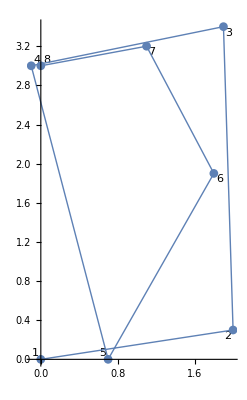

Nnodes = {{0.,0.},{0.7,0.},{2.,0.3},{1.8,1.9},{0.,3.},{-0.1,3.},{1.1,3.2},{1.9,3.4}}

Length[nnodes] = 8

topol = {{1,2,3,4,5,6,7,8}}

xi = -0.990575

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = 0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = 0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = 0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = 0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = 0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = 0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = 0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = 0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = 0.

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = -0.178484

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = -0.351232

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = -0.512691

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = -0.657671

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = -0.781514

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = -0.880239

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = -0.950676

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.990575

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.950676

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.880239

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.781514

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.657671

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.512691

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.351232

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = -0.178484

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.178484

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.351232

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.512691

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.657671

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.781514

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.880239

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.950676

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

xi = 0.990575

eta = -0.990575

elcoords = {{0.,0.},{2.,0.3},{1.9,3.4},{-0.1,3.},{0.7,0.},{1.8,1.9},{1.1,3.2},{0.,3.}}

(93.4344 | -4.30094 | 1.40766 | 1.29322 | -1.3692 | -1.113 | -15.4222 | 4.45739 | -126.481 | 0.390266 | 4.01492 | -1.9077 | -14.237 | 0.569395 | 28.6404 | -12.2459
-4.30094 | 39.2487 | 0.781313 | -1.39405 | -1.113 | 1.21433 | 4.9693 | -13.4801 | 2.43788 | -41.5288 | -1.9077 | 3.3994 | 0.569395 | -10.219 | -14.2935 | 18.6016
1.40766 | 0.781313 | 28.9509 | -8.94308 | 24.2507 | -1.48275 | -0.957735 | 0.853287 | -82.5306 | 18.6737 | 12.4547 | -2.43142 | -23.3826 | 2.8503 | -15.3541 | 4.52105
1.29322 | -1.39405 | -8.94308 | 17.5912 | -1.99465 | 7.67553 | 0.853287 | -0.380133 | 16.6261 | -32.4771 | -0.383806 | -1.30108 | 2.8503 | -8.79816 | 4.52105 | -8.40094
-1.3692 | -1.113 | 24.2507 | -1.99465 | -91.285 | 15.1548 | 17.4654 | -2.74934 | 80.5804 | -3.78928 | 34.9532 | -6.22249 | 29.9634 | -7.92586 | 30.3039 | 0.728049
-1.113 | 1.21433 | -1.48275 | 7.67553 | 15.1548 | -57.7342 | -3.26124 | 10.2971 | -3.78928 | 31.7946 | -8.27011 | 29.1017 | -5.87824 | 26.9933 | 0.728049 | 9.53237
-15.4222 | 4.9693 | -0.957735 | 0.853287 | 17.4654 | -3.26124 | -38.1136 | 11.4422 | 9.63478 | 2.01204 | -8.83597 | 3.06772 | 0.635739 | 6.96546 | 26.3194 | -14.5422
4.45739 | -13.4801 | 0.853287 | -0.380133 | -2.74934 | 10.2971 | 11.4422 | -44.7333 | 2.01204 | 5.10808 | 3.06772 | -3.15646 | 4.91784 | -10.7773 | -12.4946 | 55.1278
-126.481 | 2.43788 | -82.5306 | 16.6261 | 80.5804 | -3.78928 | 9.63478 | 2.01204 | 415.038 | -36.6929 | -168.355 | -9.03578 | 34.2904 | -11.426 | -32.2135 | 19.7588
0.390266 | -41.5288 | 18.6737 | -32.4771 | -3.78928 | 31.7946 | 2.01204 | 5.10808 | -36.6929 | 145.491 | -9.03578 | -67.8856 | -11.426 | 27.0049 | 19.7588 | -51.0069
4.01492 | -1.9077 | 12.4547 | -0.383806 | 34.9532 | -8.27011 | -8.83597 | 3.06772 | -168.355 | -9.03578 | 78.5616 | 9.62709 | 10.1689 | 6.56109 | -92.1478 | 5.94303
-1.9077 | 3.3994 | -2.43142 | -1.30108 | -6.22249 | 29.1017 | 3.06772 | -3.15646 | -9.03578 | -67.8856 | 9.62709 | 17.8727 | 6.56109 | 6.15967 | 5.94303 | -46.22
-14.237 | 0.569395 | -23.3826 | 2.8503 | 29.9634 | -5.87824 | 0.635739 | 4.91784 | 34.2904 | -11.426 | 10.1689 | 6.56109 | -62.5362 | 28.0134 | 37.5646 | -34.2153
0.569395 | -10.219 | 2.8503 | -8.79816 | -7.92586 | 26.9933 | 6.96546 | -10.7773 | -11.426 | 27.0049 | 6.56109 | 6.15967 | 28.0134 | -64.0843 | -34.2153 | 72.8218
28.6404 | -14.2935 | -15.3541 | 4.52105 | 30.3039 | 0.728049 | 26.3194 | -12.4946 | -32.2135 | 19.7588 | -92.1478 | 5.94303 | 37.5646 | -34.2153 | -41.3148 | 31.664
-12.2459 | 18.6016 | 4.52105 | -8.40094 | 0.728049 | 9.53237 | -14.5422 | 55.1278 | 19.7588 | -51.0069 | 5.94303 | -46.22 | -34.2153 | 72.8218 | 31.664 | -114.86)

```mathematica
order=2;
young=43;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

allcoords={{{0,0},{2,0.3},{1.9,3.4},{-0.1,3},{0.7,0},{1.8,1.9},{1.1,3.2},{0,3}}}
nnodes=Flatten[allcoords,1];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]

forcing=0;
{KE,FE}=Assemble[allcoords,order,forcing];
KE//MatrixForm
```

```mathematica
{psis,dpsi,Jac,x,y}=ComputeData[-1,-1,allcoords[[1]],order]//Simplify;
```

```mathematica
{x,y}/.{xi->-1,eta->0}
Det[Jac]
```

{0.,3.}

1.55-5.405 eta+0.06 eta^2+0.815 eta^3-2.2175 xi+3.705 eta xi+4.5475 eta^2 xi-3.28 eta^3 xi-0.25 xi^2+2.08375 eta xi^2-0.52125 eta^2 xi^2+1.0425 eta^3 xi^2-0.665 xi^3+0.05 eta xi^3-0.695 eta^2 xi^3

{{{2,1},{3.5,1.5},{5,2},{4.5,4},{4,6},{2.5,5},{1,4},{1.5,2.5}}}

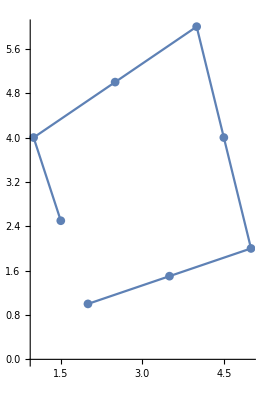

Nnodes = {{2.,1.},{3.5,1.5},{5.,2.},{1.5,2.5},{4.5,4.},{1.,4.},{2.5,5.},{4.,6.}}

Length[nnodes] = 8

topol = {{1,2,3,4,5,6,7,8}}

KE = (4.12419 | -1.34763 | -1.17766 | 0.26126 | 0.592072 | -0.0682913 | -1.86653 | 0.245263 | 2.96256 | -0.645658 | -0.804949 | 0.132204 | -1.25409 | 0.177933 | -2.30531 | 1.42632
-1.34763 | 2.45169 | 0.232371 | -0.581077 | -0.0682913 | 0.342748 | 0.274152 | -1.14767 | -0.530103 | 1.42848 | 0.132204 | -0.358919 | 0.177933 | -0.993279 | 1.31076 | -1.20809
-1.17766 | 0.232371 | -1.30813 | 0.0368978 | -0.390411 | 0.230921 | 0.182735 | -0.0524926 | 3.65932 | -0.16085 | -2.31646 | -0.0583208 | -1.36012 | 0.142863 | -0.385362 | -0.0572891
0.26126 | -0.581077 | 0.0368978 | -0.570477 | 0.202032 | -0.337338 | -0.0524926 | 0.136121 | -0.276406 | 1.48244 | 0.0572347 | -0.630186 | 0.142863 | -0.502411 | -0.0572891 | -0.0348259
0.592072 | -0.0682913 | -0.390411 | 0.202032 | 0.569913 | -0.145803 | -0.0367612 | 0.173801 | -1.48223 | 0.158779 | -0.238447 | 0.134126 | 2.35347 | -0.424962 | 0.111675 | -0.374946
-0.0682913 | 0.342748 | 0.230921 | -0.337338 | -0.145803 | 0.159552 | 0.144912 | 0.0986957 | 0.158779 | -0.602038 | 0.01857 | 0.0632149 | -0.309406 | 1.1985 | -0.374946 | -0.172285
-1.86653 | 0.274152 | 0.182735 | -0.0524926 | -0.0367612 | 0.144912 | 0.298998 | -0.797618 | -0.275436 | 0.240099 | -0.240197 | 0.0856216 | -0.531677 | -0.402695 | 2.00677 | 0.863369
0.245263 | -1.14767 | -0.0524926 | 0.136121 | 0.173801 | 0.0986957 | -0.797618 | 0.128133 | 0.240099 | -0.238438 | 0.0856216 | -0.204876 | -0.51825 | -0.61546 | 0.978925 | 1.59794
2.96256 | -0.530103 | 3.65932 | -0.276406 | -1.48223 | 0.158779 | -0.275436 | 0.240099 | -6.71796 | 0.119307 | 9.09962 | -0.927696 | -0.400207 | 0.534052 | -3.39795 | 0.627499
-0.645658 | 1.42848 | -0.16085 | 1.48244 | 0.158779 | -0.602038 | 0.240099 | -0.238438 | 0.119307 | -2.30283 | -0.927696 | 3.45288 | 0.534052 | -0.419405 | 0.627499 | -1.8603
-0.804949 | 0.132204 | -2.31646 | 0.0572347 | -0.238447 | 0.01857 | -0.240197 | 0.0856216 | 9.09962 | -0.927696 | -8.44177 | 0.850698 | -1.05267 | 0.269409 | -1.19237 | -0.0988314
0.132204 | -0.358919 | -0.0583208 | -0.630186 | 0.134126 | 0.0632149 | 0.0856216 | -0.204876 | -0.927696 | 3.45288 | 0.850698 | -3.65285 | 0.269409 | -0.0919651 | -0.0988314 | -0.589829
-1.25409 | 0.177933 | -1.36012 | 0.142863 | 2.35347 | -0.309406 | -0.531677 | -0.51825 | -0.400207 | 0.534052 | -1.05267 | 0.269409 | 0.825694 | -1.04329 | 2.09968 | 0.95344
0.177933 | -0.993279 | 0.142863 | -0.502411 | -0.424962 | 1.1985 | -0.402695 | -0.61546 | 0.534052 | -0.419405 | 0.269409 | -0.0919651 | -1.04329 | 0.0194359 | 0.95344 | 2.06898
-2.30531 | 1.31076 | -0.385362 | -0.0572891 | 0.111675 | -0.374946 | 2.00677 | 0.978925 | -3.39795 | 0.627499 | -1.19237 | -0.0988314 | 2.09968 | 0.95344 | 5.38016 | -4.86743
1.42632 | -1.20809 | -0.0572891 | -0.0348259 | -0.374946 | -0.172285 | 0.863369 | 1.59794 | 0.627499 | -1.8603 | -0.0988314 | -0.589829 | 0.95344 | 2.06898 | -4.86743 | 1.3437)

FE = (0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0
0.
0)

```mathematica
order=2;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{2,1},{3.5,1.5},{5,2},{4.5,4},{4,6},{2.5,5},{1,4},{1.5,2.5}}}
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True]
{KE,FE}=Assemble[allcoords,2,1];

Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineDirichlet[EK_,EF_,nodes_,allcoords_,order_,id1_,id2_,ek_,ef_]:=Block[{Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k,newnodes},

(*{els,ids}=DefineLineNodes[id1,id2,nodes];*)
{els,ids,newnodes}=DefineLineNodes[id1,id2,nodes,allcoords,order];

(*Print["newnodes = ",newnodes];

Print["els = ",els];
Print["ids = ",ids];
Print["nodes = ",nodes];
Print["id1 = ",id1];
Print["id2 = ",id2];*)

el=Length[els];
Print["newnodes = ",newnodes];
For[i=1,i≤el+1,i++,

For[j=1,j≤2,j++,
For[k=1,k≤2,k++,

Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];


];
{Ek,Ef}
];
```

```mathematica
(*Dado dois ids extremos, retorna uma topologia e as coordenas completas intermediárias aos nós de um elemento linear*)
DefineLineNodes[id1_,id2_,nnodes_,allcoords_,order_]:=Block[{vert=True,w,k,newnodes,A,B,tol,linenodes,i,ids,elss,nels=Length[allcoords],topol,elss1,linearelcoordsvec},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
topol=ComputeTopol[allcoords,order];
For[i=1,i≤Length[nnodes],i++,

(*x=x Linha vertical*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,

If[Between[nnodes[[i]][[2]],{A[[2]],B[[2]]}],
AppendTo[linenodes,nnodes[[i]]];

AppendTo[ids,i];
];

];

(*y=y Linha horizontal*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{A[[1]],B[[1]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];
vert=False;
];

];
elss1={};
For[i=1,i<Length[ids],i++,

AppendTo[elss1,{nnodes[[ ids[[i]] ]],nnodes[[ ids[[i+1]] ]]} ];

];

nels=Length[allcoords];
linearelcoordsvec={};
For[iel=1,iel≤nels,iel++,
linearelcoords={};
For[nn=1,nn≤order 4,nn++,
For[id=1,id≤Length[ids],id++,
If[topol[[iel,nn]]==ids[[id]],
(*Print["iel = ",iel];
Print["nn = ",nn];
Print["ids[[id]] = ",ids[[id]]];*)
AppendTo[linearelcoords,allcoords[[iel,nn]]];
];
];

];
If[Length[linearelcoords]≠0,
AppendTo[linearelcoordsvec,linearelcoords];

];
];
(*Print["id = ",ids];
Print["topol = ",topol];
Print["linearelcoordsvec = ",linearelcoordsvec];*)
(*elss={};
For[i=1,i≤nels,i++,
For[j=1,j≤1Length[ids],j++,
For[k=1,k≤4order,k++,
If[topol[[i]][[k]]==ids[[j]],
AppendTo[elss,{i,k}];
];
];
];
];


nels=elss[[ Length[elss] ]][[1]];
newnodes=Table[0,{nels},{order+1}];
k=1;
ids={};
nels=Length[allcoords];
For[w=1,w≤nels,w++,
For[i=1,i≤order+1,i++,
newnodes[[w]][[i]]=allcoords[[w,elss[[i,2]]]];
AppendTo[ids,elss[[i,2]]];
];
k++;
];
*)
{elss1,ids,linearelcoordsvec}
];
```

{{2,1},{3.5,1.5},{5,2},{4.5,4},{4,6},{2.5,5},{1,4},{1.5,2.5}}

```mathematica
nnodes
```

nnodes

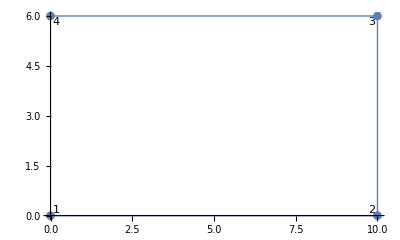

Length[nnodes] = 4

topol = {{1,2,3,4}}

8

KE = (4.33455×10^18 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^18 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^18 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^18 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

FE = (0
0
6000
0
6000.
0
0
0)

{6.92113×10^-13,-1.81723×10^-28,11.,3.02872×10^-29,11.,5.82,6.92113×10^-13,5.82}

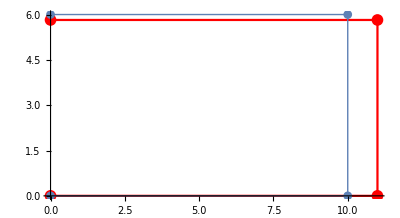

Length[nnodes] = 4

topol = {{1,2,3,4}}

8

KE = (4.33455×10^18 | 1.78571×10^6 | -1.12943×10^6 | -137363. | -2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363.
1.78571×10^6 | 6.87424×10^18 | 137363. | 2.28327×10^6 | -1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6
-1.12943×10^6 | 137363. | 4.33455×10^6 | -1.78571×10^6 | -1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6
-137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^18 | 137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6
-2.16728×10^6 | -1.78571×10^6 | -1.03785×10^6 | 137363. | 4.33455×10^6 | 1.78571×10^6 | -1.12943×10^6 | -137363.
-1.78571×10^6 | -3.43712×10^6 | -137363. | -5.72039×10^6 | 1.78571×10^6 | 6.87424×10^6 | 137363. | 2.28327×10^6
-1.03785×10^6 | -137363. | -2.16728×10^6 | 1.78571×10^6 | -1.12943×10^6 | 137363. | 4.33455×10^18 | -1.78571×10^6
137363. | -5.72039×10^6 | 1.78571×10^6 | -3.43712×10^6 | -137363. | 2.28327×10^6 | -1.78571×10^6 | 6.87424×10^6)

FE = (0
0
6000
0
6000.
0
0
0)

{6.92113×10^-13,-1.81723×10^-28,11.,3.02872×10^-29,11.,5.82,6.92113×10^-13,5.82}

-Graphics-

```mathematica
order=1;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));


allcoords=CreateRectangularMesh[{0,0},{10,6},0,0,order];
nnodes=ComputeNNodes[allcoords]//N;

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]



forcing=0;
{KE,FE}=Assemble[allcoords,order,forcing];


(*Dirichlet - ux=0 vy=0 no no 1*)
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,2,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,4,0,{{10^12,1},{1,1}},{0,0}];

(*Newman - fx=6000 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{6000,0}];

(*Newman - fx=6000 no no 3*)
{KE,FE}=ApplyNodeBC[KE,FE,3,1,{{1,1},{1,1}},{6000,0}];



Length[KE]
Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]

sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=500;
deformed=(Flatten[nnodes]+scale sol)

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

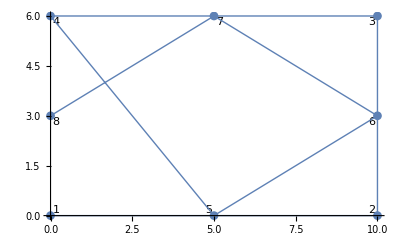

Nnodes = {{0.,0.},{5.,0.},{10.,0.},{10.,3.},{0.,3.},{10.,6.},{5.,6.},{0.,6.}}

Length[nnodes] = 8

topol = {{1,2,3,4,5,6,7,8}}

KE = (9.26967×10^18 | -1.64748×10^6 | 1.36225×10^6 | -309934. | -4.00406×10^6 | 2.20817×10^6 | -608585. | 276029. | -3.65161×10^6 | -152294. | 372635. | -1.78271×10^6 | 2.47567×10^6 | -1.74543×10^6 | 1.12354×10^6 | -2.55197×10^6
-1.64748×10^6 | 1.22484×10^19 | -309934. | 533949. | 2.08913×10^6 | -5.6312×10^6 | 395076. | -182312. | 323896. | 843106. | -1.78271×10^6 | 2.60906×10^6 | -1.74543×10^6 | 2.13328×10^6 | -3.02816×10^6 | -3.1851×10^6
1.36225×10^6 | -309934. | 2.11191×10^7 | -4.61689×10^6 | -54803.1 | -217111. | -1.81354×10^6 | 767180. | 646775. | 1.70252×10^6 | -2.51724×10^7 | 5.98807×10^6 | 1.32837×10^7 | -2.34399×10^6 | 5.11948×10^6 | 456912.
-309934. | 533949. | -4.61689×10^6 | 4.18832×10^18 | -98063.5 | 509740. | 648132. | -649437. | 1.70252×10^6 | -233032. | 5.51188×10^6 | -5.00312×10^6 | -1.8678×10^6 | 2.84314×10^6 | 456912. | 7.53274×10^6
-4.00406×10^6 | 2.08913×10^6 | -54803.1 | -98063.5 | -5.01917×10^6 | 3.29885×10^6 | 687021. | -247965. | 1.30505×10^7 | -6.5767×10^6 | 516544. | -246729. | 1.77865×10^6 | -998089. | 1.81267×10^6 | -1.00173×10^6
2.20817×10^6 | -5.6312×10^6 | -217111. | 509740. | 3.29885×10^6 | -8.28446×10^6 | -247965. | 459340. | -7.05289×10^6 | 1.94986×10^7 | 229462. | -3.00944×10^6 | -998089. | 4.06976×10^6 | -1.00173×10^6 | 2.58366×10^6
-608585. | 395076. | -1.81354×10^6 | 648132. | 687021. | -247965. | 6.22701×10^18 | -3.20762×10^6 | -2.25836×10^6 | 587488. | -745973. | 311900. | 289064. | -344957. | -1.08824×10^7 | 4.43205×10^6
276029. | -182312. | 767180. | -649437. | -247965. | 459340. | -3.20762×10^6 | 6.93156×10^6 | 587488. | -4.41859×10^6 | 311900. | -2.96403×10^6 | -821148. | 8.72685×10^6 | 4.90824×10^6 | -2.1335×10^7
-3.65161×10^6 | 323896. | 646775. | 1.70252×10^6 | 1.30505×10^7 | -7.05289×10^6 | -2.25836×10^6 | 587488. | 2.45439×10^6 | 1.10596×10^6 | -6.43526×10^6 | -1.72502×10^6 | -5.54983×10^6 | 6.37816×10^6 | -1.51604×10^7 | 7.61378×10^6
-152294. | 843106. | 1.70252×10^6 | -233032. | -6.5767×10^6 | 1.94986×10^7 | 587488. | -4.41859×10^6 | 1.10596×10^6 | -1.37928×10^19 | -1.72502×10^6 | -2.79298×10^6 | 6.37816×10^6 | -1.51523×10^7 | 7.61378×10^6 | -2.88084×10^7
372635. | -1.78271×10^6 | -2.51724×10^7 | 5.51188×10^6 | 516544. | 229462. | -745973. | 311900. | -6.43526×10^6 | -1.72502×10^6 | 2.71947×10^7 | -5.45757×10^6 | -1.0071×10^7 | 1.15747×10^6 | -6.59388×10^6 | -3.65438×10^6
-1.78271×10^6 | 2.60906×10^6 | 5.98807×10^6 | -5.00312×10^6 | -246729. | -3.00944×10^6 | 311900. | -2.96403×10^6 | -1.72502×10^6 | -2.79298×10^6 | -5.45757×10^6 | 6.57538×10^6 | 1.15747×10^6 | 1.66733×10^6 | -3.65438×10^6 | 2.03691×10^6
2.47567×10^6 | -1.74543×10^6 | 1.32837×10^7 | -1.8678×10^6 | 1.77865×10^6 | -998089. | 289064. | -821148. | -5.54983×10^6 | 6.37816×10^6 | -1.0071×10^7 | 1.15747×10^6 | 6.99566×10^6 | 3.70534×10^6 | 3.05534×10^6 | 784605.
-1.74543×10^6 | 2.13328×10^6 | -2.34399×10^6 | 2.84314×10^6 | -998089. | 4.06976×10^6 | -344957. | 8.72685×10^6 | 6.37816×10^6 | -1.51523×10^7 | 1.15747×10^6 | 1.66733×10^6 | 3.70534×10^6 | 1.99185×10^6 | 784605. | 501784.
1.12354×10^6 | -3.02816×10^6 | 5.11948×10^6 | 456912. | 1.81267×10^6 | -1.00173×10^6 | -1.08824×10^7 | 4.90824×10^6 | -1.51604×10^7 | 7.61378×10^6 | -6.59388×10^6 | -3.65438×10^6 | 3.05534×10^6 | 784605. | 1.86227×10^19 | -1.14421×10^7
-2.55197×10^6 | -3.1851×10^6 | 456912. | 7.53274×10^6 | -1.00173×10^6 | 2.58366×10^6 | 4.43205×10^6 | -2.1335×10^7 | 7.61378×10^6 | -2.88084×10^7 | -3.65438×10^6 | 2.03691×10^6 | 784605. | 501784. | -1.14421×10^7 | 3.44621×10^7)

FE = (0
0
4000
0
4000.
0
0
0
0
0
4000.
0
0.
0
0
0)

16

16

{3.07045×10^-13,-3.94361×10^-13,9.43642,1.02329×10^-12,11.1456,5.2451,-2.22142×10^-13,5.11482,5.57381,1.04895×10^-12,10.4522,3.28184,6.89503,5.61719,2.65245×10^-13,2.41631}

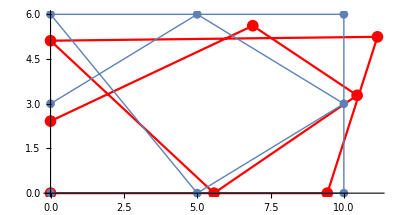

```mathematica
order=2;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

allcoords=CreateRectangularMesh[{0,0},{10,6},0,0,order];
nnodes=Flatten[allcoords,1];

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]

forcing=0;
{KE,FE}=Assemble[allcoords,order,forcing];

(*Dirichlet - ux=0 vy=0 no no 1*)
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,2,0,{{1,1},{1,10^12}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,4,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet - ux=0 no no 4*)
{KE,FE}=ApplyNodeBC[KE,FE,8,0,{{10^12,1},{1,1}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,5,0,{{1,1},{1,10^12}},{0,0}];


(*Newman - fx=6000 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{4000,0}];

(*Newman - fx=6000 no no 3*)
{KE,FE}=ApplyNodeBC[KE,FE,3,1,{{1,1},{1,1}},{4000,0}];

(*Newman - fx=6000 no no 3*)
{KE,FE}=ApplyNodeBC[KE,FE,6,1,{{1,1},{1,1}},{4000,0}];
Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]
Length[KE]
Length[FE]


sol=LinearSolve[KE,FE,Method->"Banded"];
scale=1000;
deformed=(Flatten[nnodes]+scale sol)

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];

defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

```mathematica
(KE.sol-FE)//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
10000 0.2 6/3
```

4000.

```mathematica
sol//Chop
```

{0,0,0.000719754,0,0.000101238,0.0000615301,0,0.000195315,0.000578369,0,0.000674732,-0.000534745,-0.000106461,-0.000105786,0,-0.00021232}

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineNewman[EF_,fx_,order_,nodes_,id1_,id2_,fxorfy_,allcoords_]:=Block[{Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,newnodes},

(*{els,ids}=DefineLineNodes[id1,id2,nodes];*)
{els,ids,newnodes}=DefineLineNodes[id1,id2,nodes,allcoords,order];
(*Print["els = ",els];
Print["ids = ",ids];
Print["newnodes = ",newnodes];*)

el=Length[newnodes];
k=0;
For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];

If[fxorfy==1,(*fy*)
co={els[[i]][[1,1]],els[[i]][[2,1]]};
co={newnodes[[el-k]][[1,1]],newnodes[[el-k]][[2,1]]};
(*co={newnodes[[el-k]][[1,1]],newnodes[[el-k]][[2,1]]};*)
(*newco={newnodes[[el-k]][[1,1]],newnodes[[el-k]][[2,1]]};

Print["co = ",co];*)
,
(*fx*)
co={els[[i]][[1,2]],els[[i]][[2,2]]};
co={newnodes[[el-k]][[1,2]],newnodes[[el-k]][[2,2]]};
(*co={newnodes[[i]][[1,2]],newnodes[[i]][[2,2]]};*)
(*newco={newnodes[[i]][[1,2]],newnodes[[i]][[2,2]]};*)
];
k++;
(*Print["Co = ",co];*)
(*newco=co;*)

(*newco=newnodes[[i]];*)
Print["co = ",co];
newco=ComputeNewLinearNodes[order,co];
newco=SortBy[newco,Small];
(*newco={co[[2]],co[[2]]+(co[[1]]-co[[2]])/2,co[[1]]};
Print["newco = ",newco];*)
Print["newco = ",newco];
xx=Sum[shapes[[i]] newco[[i]],{i,1,order+1}];
J=D[xx,xi];
Print["J = ",J];
vecPtosPesos=GaussianQuadratureWeights[4 order+2,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]] J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];

ids=Sort[ids,Greater];
Print["ids = ",ids];
Print["integralxi1 = ",integralxi1];

If[fxorfy==1,(*fy*)
Print["ids[[i]]) 2 = ",(ids[[i]]) 2];
Print["ids[[i+1]]) 2 = ",(ids[[i+1]]) 2];
Print["ids[[i+2]]) 2 = ",(ids[[i+2]]) 2];
Ef[[ (ids[[i]]) 2]]+=integralxi1[[1]];
Ef[[ (ids[[i+1]]) 2]]+=integralxi1[[2]];
Ef[[ (ids[[i+2]]) 2]]+=integralxi1[[3]];
,
(*fx*)
Ef[[ ids[[i]]2-1 ]]+=integralxi1[[1]];
Ef[[ ids[[i]]2 ]]+=integralxi1[[2]];
];
];
Ef
];
```

```mathematica
allcoords
```

{{{0,0},{10,0},{10,6},{0,6},{5,0},{10,3},{5,6},{0,3}}}

{{0.,0.},{2.,0.},{4.,0.},{6.,0.},{8.,0.},{8.,1.},{4.,1.},{0.,1.},{8.,2.},{6.,2.},{4.,2.},{2.,2.},{0.,2.},{8.,3.},{4.,3.},{0.,3.},{8.,4.},{6.,4.},{4.,4.},{2.,4.},{0.,4.}}

Length[nnodes] = 21

topol = {{1,3,11,13,2,7,12,8},{3,5,9,11,4,6,10,7},{13,11,19,21,12,15,20,16},{11,9,17,19,10,14,18,15}}

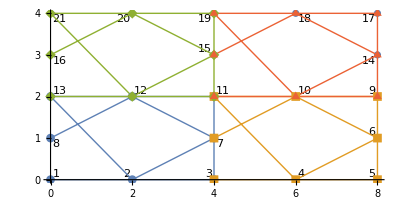

newnodes = {{{0,0},{4,0},{2,0}},{{4,0},{8,0},{6,0}}}

newnodes = {{{8,0},{8,2},{8,1}},{{8,2},{8,4},{8,3}}}

(2.08651×10^7 | -3.80188×10^6 | -6.30644×10^6 | -351448. | 2.63901×10^6 | -715233. | 0 | 0 | 0 | 0 | 0 | 0 | 1.55314×10^6 | -4.11395×10^6 | 952977. | -5.88917×10^6 | 0 | 0 | 0 | 0 | -9.12766×10^6 | 5.09579×10^6 | 5.18844×10^6 | -4.02792×10^6 | -1.16×10^6 | 636989. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3.80188×10^6 | 3.2237×10^19 | 747453. | 3.66675×10^6 | -715233. | 1.08194×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | -4.11395×10^6 | 7.40752×10^6 | -6.98807×10^6 | -9.5757×10^6 | 0 | 0 | 0 | 0 | 4.82106×10^6 | -1.49079×10^7 | -4.02792×10^6 | 5.324×10^6 | 911715. | -321003. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-6.30644×10^6 | 747453. | -224969. | 2.55222×10^6 | 1.08875×10^6 | 3.92888×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | -1.2558×10^7 | -3.98082×10^6 | -3.70866×10^7 | 1.75703×10^7 | 0 | 0 | 0 | 0 | 3.01362×10^7 | -1.62759×10^7 | -1.5131×10^7 | 1.47188×10^7 | -5.5675×10^6 | 1.35574×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-351448. | 3.66675×10^6 | 2.55222×10^6 | -4.06531×10^19 | 3.92888×10^6 | -891130. | 0 | 0 | 0 | 0 | 0 | 0 | -3.98082×10^6 | -5.89243×10^6 | 1.75703×10^7 | -7.80634×10^7 | 0 | 0 | 0 | 0 | -1.5177×10^7 | 5.18948×10^7 | 1.47188×10^7 | -4.1877×10^7 | 1.35574×10^6 | -1.19959×10^7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.63901×10^6 | -715233. | 1.08875×10^6 | 3.92888×10^6 | 8.74301×10^7 | -2.63013×10^7 | -1.051×10^7 | 1.05709×10^7 | -6.51098×10^6 | 1.52862×10^6 | -1.96019×10^7 | 1.99466×10^6 | -4.61333×10^7 | 9.4136×10^6 | 1.17827×10^7 | 1.05441×10^6 | 1.40687×10^7 | -2.88255×10^6 | -1.18395×10^7 | 400068. | 3.30356×10^6 | -110055. | 2.4936×10^7 | -5.40921×10^6 | -3.49254×10^6 | 1.77042×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-715233. | 1.08194×10^6 | 3.92888×10^6 | -891130. | -2.63013×10^7 | 1.17311×10^20 | 1.16698×10^7 | -6.54214×10^6 | 1.52862×10^6 | -1.80657×10^7 | 1.99466×10^6 | -5.25509×10^7 | 7.2158×10^6 | -4.69186×10^6 | 1.05441×10^6 | 2.00219×10^7 | -3.15728×10^6 | 3.69714×10^7 | 400068. | -3.22187×10^7 | 439395. | 1.13948×10^7 | -4.31031×10^6 | 3.72594×10^6 | 1.49569×10^6 | -1.26309×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.051×10^7 | 1.16698×10^7 | -1.22922×10^8 | 1.43635×10^7 | 3.3112×10^7 | -7.27911×10^6 | 1.71672×10^8 | -3.97352×10^7 | -7.51802×10^7 | 2.60329×10^7 | 0 | 0 | -8.32284×10^7 | 1.62737×10^7 | 3.67041×10^7 | -5.26001×10^6 | -1.71064×10^7 | 2.43081×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.05709×10^7 | -6.54214×10^6 | 1.43635×10^7 | -3.63971×10^20 | -7.27911×10^6 | 8.80983×10^7 | -3.97352×10^7 | 4.6843×10^8 | 2.60329×10^7 | -1.92426×10^8 | 0 | 0 | 1.73726×10^7 | -2.2874×10^8 | -5.26001×10^6 | 9.28225×10^7 | 2.43081×10^6 | -4.60408×10^7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -6.51098×10^6 | 1.52862×10^6 | 3.3112×10^7 | -7.27911×10^6 | -1.37132×10^19 | -806683. | -1.92223×10^7 | 7.62145×10^6 | 1.32035×10^7 | 623898. | 0 | 0 | 1.7412×10^7 | -4.24125×10^6 | -1.85251×10^7 | 4.2538×10^6 | 7.96865×10^6 | -838528. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.52862×10^6 | -1.80657×10^7 | -7.27911×10^6 | 8.80983×10^7 | -806683. | -3.32335×10^19 | 6.52255×10^6 | -6.97942×10^7 | 623898. | 3.72736×10^7 | 0 | 0 | -3.96652×10^6 | 5.11638×10^7 | 5.35271×10^6 | -4.35799×10^7 | -1.11325×10^6 | 1.96655×10^7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.96019×10^7 | 1.99466×10^6 | 1.71672×10^8 | -3.97352×10^7 | -1.92223×10^7 | 6.52255×10^6 | -2.12699×10^20 | 5.56087×10^7 | 2.83831×10^7 | -1.23137×10^7 | 0 | 0 | 9.53982×10^7 | -2.34572×10^7 | -1.98514×10^6 | -5.28502×10^6 | -1.25522×10^6 | 501316. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.99466×10^6 | -5.25509×10^7 | -3.97352×10^7 | 4.6843×10^8 | 7.62145×10^6 | -6.97942×10^7 | 5.56087×10^7 | -5.24881×10^8 | -1.23137×10^7 | 8.49154×10^7 | 0 | 0 | -2.45561×10^7 | 2.44097×10^8 | -5.28502×10^6 | -2.71695×10^7 | 501316. | 3.05545×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.55314×10^6 | -4.11395×10^6 | -1.2558×10^7 | -3.98082×10^6 | -4.61333×10^7 | 7.2158×10^6 | -7.51802×10^7 | 2.60329×10^7 | 1.32035×10^7 | 623898. | 2.83831×10^7 | -1.23137×10^7 | 9.04799×10^7 | -2.42576×10^7 | -1.12142×10^7 | -8.43318×10^6 | 1.36898×10^6 | -3.77884×10^6 | 2.17051×10^7 | -237790. | -5.69367×10^7 | 9.94118×10^6 | -1.76149×10^7 | 2.67108×10^6 | -2.3468×10^6 | 719770. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.11395×10^6 | 7.40752×10^6 | -3.98082×10^6 | -5.89243×10^6 | 9.4136×10^6 | -4.69186×10^6 | 2.60329×10^7 | -1.92426×10^8 | 623898. | 3.72736×10^7 | -1.23137×10^7 | 8.49154×10^7 | -2.42576×10^7 | 1.1934×10^8 | -8.43318×10^6 | 8.10669×10^6 | -3.77884×10^6 | -3.67875×10^6 | -237790. | 6.10517×10^7 | 7.74338×10^6 | -1.63461×10^8 | 2.67108×10^6 | 8.21309×10^6 | 719770. | -8.30645×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
952977. | -6.98807×10^6 | -3.70866×10^7 | 1.75703×10^7 | 1.17827×10^7 | 1.05441×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | -1.12142×10^7 | -8.43318×10^6 | 4.5244×10^7 | -2.6405×10^7 | 0 | 0 | 0 | 0 | 4.14376×10^6 | -2.31167×10^6 | 5.6841×10^6 | 1.81063×10^6 | -2.68428×10^7 | 1.13267×10^7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5.88917×10^6 | -9.5757×10^6 | 1.75703×10^7 | -7.80634×10^7 | 1.05441×10^6 | 2.00219×10^7 | 0 | 0 | 0 | 0 | 0 | 0 | -8.43318×10^6 | 8.10669×10^6 | -2.6405×10^7 | 9.32192×10^7 | 0 | 0 | 0 | 0 | -2.31167×10^6 | 6.84816×10^6 | 1.81063×10^6 | 417658. | 1.02278×10^7 | -5.79288×10^7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.40687×10^7 | -3.15728×10^6 | -8.32284×10^7 | 1.73726×10^7 | 1.7412×10^7 | -3.96652×10^6 | 9.53982×10^7 | -2.45561×10^7 | 1.36898×10^6 | -3.77884×10^6 | 0 | 0 | -3.27278×10^20 | 1.31267×10^8 | 3.29562×10^6 | 8.42906×10^6 | -4.56099×10^6 | -190814. | 0 | 0 | 0 | 0 | 4.43321×10^8 | -1.94005×10^8 | -1.45599×10^7 | 7.503×10^6 | 0 | 0 | -7.23105×10^7 | 3.29309×10^7 | -1.38669×10^8 | 6.00149×10^7 | 2.9488×10^7 | -1.24415×10^7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2.88255×10^6 | 3.69714×10^7 | 1.62737×10^7 | -2.2874×10^8 | -4.24125×10^6 | 5.11638×10^7 | -2.34572×10^7 | 2.44097×10^8 | -3.77884×10^6 | -3.67875×10^6 | 0 | 0 | 1.31267×10^8 | -4.12375×10^8 | 8.42906×10^6 | 3.36968×10^7 | -190814. | -1.40373×10^7 | 0 | 0 | 0 | 0 | -1.95104×10^8 | 3.99906×10^8 | 7.503×10^6 | -2.18358×10^7 | 0 | 0 | 3.32056×10^7 | -7.20608×10^7 | 6.11138×10^7 | -9.44638×10^7 | -1.27162×10^7 | 1.92251×10^7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1.18395×10^7 | 400068. | 3.67041×10^7 | -5.26001×10^6 | -1.85251×10^7 | 5.35271×10^6 | -1.98514×10^6 | -5.28502×10^6 | 2.17051×10^7 | -237790. | 0 | 0 | 3.29562×10^6 | 8.42906×10^6 | -6.09535×10^7 | -324205. | 5.13246×10^7 | 3.52906×10^6 | 0 | 0 | 0 | 0 | -2.38937×10^7 | 1.66801×10^7 | -7.62784×10^7 | 3.70954×10^7 | 0 | 0 | 8.58975×10^7 | -4.93435×10^7 | -7.21278×10^6 | 9.50782×10^6 | -5.31905×10^6 | 1.66127×10^6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 400068. | -3.22187×10^7 | -5.26001×10^6 | 9.28225×10^7 | 4.2538×10^6 | -4.35799×10^7 | -5.28502×10^6 | -2.71695×10^7 | -237790. | 6.10517×10^7 | 0 | 0 | 8.42906×10^6 | 3.36968×10^7 | -324205. | -2.30851×10^8 | 3.52906×10^6 | 1.8835×10^8 | 0 | 0 | 0 | 0 | 1.66801×10^7 | -2.36619×10^7 | 3.70954×10^7 | -1.56124×10^8 | 0 | 0 | -4.82446×10^7 | 1.43884×10^8 | 9.50782×10^6 | 899738. | 1.66127×10^6 | -1.40131×10^7 | 0 | 0 | 0 | 0
-9.12766×10^6 | 4.82106×10^6 | 3.01362×10^7 | -1.5177×10^7 | 3.30356×10^6 | 439395. | -1.71064×10^7 | 2.43081×10^6 | 7.96865×10^6 | -1.11325×10^6 | -1.25522×10^6 | 501316. | -5.69367×10^7 | 7.74338×10^6 | 4.14376×10^6 | -2.31167×10^6 | -4.56099×10^6 | -190814. | 5.13246×10^7 | 3.52906×10^6 | -3.23631×10^7 | -1.81132×10^7 | -5.49579×10^7 | 2.3386×10^6 | 1.11705×10^7 | -615038. | 8.33839×10^6 | -6.2409×10^6 | 1.5721×10^8 | -1.09099×10^7 | 1.96021×10^7 | -1.12447×10^7 | -1.15175×10^7 | 6.79611×10^6 | -2.25467×10^7 | 8.42304×10^6 | -8.30744×10^7 | 6.97619×10^6 | 1.76353×10^7 | -1.59205×10^6 | -1.1154×10^7 | 5.73573×10^6
5.09579×10^6 | -1.49079×10^7 | -1.62759×10^7 | 5.18948×10^7 | -110055. | 1.13948×10^7 | 2.43081×10^6 | -4.60408×10^7 | -838528. | 1.96655×10^7 | 501316. | 3.05545×10^6 | 9.94118×10^6 | -1.63461×10^8 | -2.31167×10^6 | 6.84816×10^6 | -190814. | -1.40373×10^7 | 3.52906×10^6 | 1.8835×10^8 | -1.81132×10^7 | -6.84936×10^7 | 2.3386×10^6 | -8.69198×10^6 | -615038. | 2.76744×10^6 | -6.2409×10^6 | 1.07928×10^7 | -1.31077×10^7 | 9.36045×10^7 | -1.12447×10^7 | 2.89658×10^7 | 6.52138×10^6 | -1.89553×10^7 | 8.42304×10^6 | -5.56808×10^7 | 7.52564×10^6 | -2.65618×10^7 | -493152. | 1.8612×10^6 | 5.46101×10^6 | -1.22436×10^7
5.18844×10^6 | -4.02792×10^6 | -1.5131×10^7 | 1.47188×10^7 | 2.4936×10^7 | -4.31031×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | -1.76149×10^7 | 2.67108×10^6 | 5.6841×10^6 | 1.81063×10^6 | 0 | 0 | 0 | 0 | -5.49579×10^7 | 2.3386×10^6 | 1.91434×10^8 | -2.68389×10^7 | -2.11064×10^7 | -1.23229×10^6 | 0 | 0 | 2.14119×10^6 | -9.9771×10^6 | -5.89827×10^6 | 5.62406×10^6 | 0 | 0 | 0 | 0 | 1.48031×10^7 | 1.35066×10^7 | -7.09615×10^7 | 3.66226×10^6 | 4.27426×10^6 | 4.43517×10^6
-4.02792×10^6 | 5.324×10^6 | 1.47188×10^7 | -4.1877×10^7 | -5.40921×10^6 | 3.72594×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 2.67108×10^6 | 8.21309×10^6 | 1.81063×10^6 | 417658. | 0 | 0 | 0 | 0 | 2.3386×10^6 | -8.69198×10^6 | -2.68389×10^7 | 8.82887×10^7 | -1.23229×10^6 | 1.89675×10^7 | 0 | 0 | -9.9771×10^6 | 3.83657×10^6 | 5.62406×10^6 | -1.97364×10^7 | 0 | 0 | 0 | 0 | 1.46055×10^7 | -1.13882×10^7 | 3.66226×10^6 | -2.2418×10^7 | 4.43517×10^6 | -5.70877×10^6
-1.16×10^6 | 911715. | -5.5675×10^6 | 1.35574×10^6 | -3.49254×10^6 | 1.49569×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | -2.3468×10^6 | 719770. | -2.68428×10^7 | 1.02278×10^7 | 0 | 0 | 0 | 0 | 1.11705×10^7 | -615038. | -2.11064×10^7 | -1.23229×10^6 | 4.66953×10^7 | -1.67833×10^7 | 0 | 0 | 1.72776×10^6 | -1.18227×10^6 | -2.70323×10^7 | 1.33789×10^7 | 0 | 0 | 0 | 0 | -1.72277×10^7 | 2.93958×10^6 | 2.50335×10^7 | -6.83892×10^6 | 90348.5 | -1.96646×10^6
636989. | -321003. | 1.35574×10^6 | -1.19959×10^7 | 1.77042×10^6 | -1.26309×10^6 | 0 | 0 | 0 | 0 | 0 | 0 | 719770. | -8.30645×10^6 | 1.13267×10^7 | -5.79288×10^7 | 0 | 0 | 0 | 0 | -615038. | 2.76744×10^6 | -1.23229×10^6 | 1.89675×10^7 | -1.67833×10^7 | 4.9332×10^7 | 0 | 0 | -1.18227×10^6 | 253743. | 1.228×10^7 | -4.31338×10^7 | 0 | 0 | 0 | 0 | 2.66486×10^6 | -9.06601×10^6 | -6.83892×10^6 | 1.65648×10^7 | -1.69173×10^6 | 5.68656×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.43321×10^8 | -1.95104×10^8 | -2.38937×10^7 | 1.66801×10^7 | 8.33839×10^6 | -6.2409×10^6 | 0 | 0 | 0 | 0 | -6.98636×10^20 | 2.99669×10^8 | 7.08125×10^6 | -4.96969×10^6 | 0 | 0 | 6.1355×10^7 | -2.08288×10^7 | 3.07848×10^8 | -1.40244×10^8 | -6.44196×10^7 | 2.90843×10^7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.94005×10^8 | 3.99906×10^8 | 1.66801×10^7 | -2.36619×10^7 | -6.2409×10^6 | 1.07928×10^7 | 0 | 0 | 0 | 0 | 2.99669×10^8 | -6.01479×10^8 | -4.96969×10^6 | 1.24883×10^7 | 0 | 0 | -2.19277×10^7 | 1.74078×10^7 | -1.40244×10^8 | 2.91758×10^8 | 2.90843×10^7 | -6.09411×10^7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.45599×10^7 | 7.503×10^6 | -7.62784×10^7 | 3.70954×10^7 | 1.5721×10^8 | -1.31077×10^7 | 2.14119×10^6 | -9.9771×10^6 | 1.72776×10^6 | -1.18227×10^6 | 7.08125×10^6 | -4.96969×10^6 | -2.69679×10^8 | 2.2917×10^7 | 1.29391×10^7 | -1.05828×10^7 | 6.01323×10^6 | -4.13696×10^6 | 1.66491×10^8 | -7.11304×10^7 | -8.9359×10^7 | 5.05867×10^7 | 9.27819×10^7 | -2.29534×10^6 | -2.38037×10^7 | 4.69351×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.503×10^6 | -2.18358×10^7 | 3.70954×10^7 | -1.56124×10^8 | -1.09099×10^7 | 9.36045×10^7 | -9.9771×10^6 | 3.83657×10^6 | -1.18227×10^6 | 253743. | -4.96969×10^6 | 1.24883×10^7 | 2.2917×10^7 | -2.95233×10^8 | -1.05828×10^7 | 1.63922×10^7 | -4.13696×10^6 | 8.16042×10^6 | -7.11304×10^7 | 3.99917×10^8 | 4.83889×10^7 | -1.88771×10^8 | -2.29534×10^6 | 3.49484×10^7 | 4.69351×10^6 | -1.43574×10^7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.96021×10^7 | -1.12447×10^7 | -5.89827×10^6 | 5.62406×10^6 | -2.70323×10^7 | 1.228×10^7 | 0 | 0 | 1.29391×10^7 | -1.05828×10^7 | 2.10506×10^8 | -1.10272×10^8 | 0 | 0 | 0 | 0 | -1.35441×10^7 | 4.47618×10^6 | -5.40739×10^7 | 2.90786×10^7 | -9.33014×10^7 | 5.04596×10^7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.12447×10^7 | 2.89658×10^7 | 5.62406×10^6 | -1.97364×10^7 | 1.33789×10^7 | -4.31338×10^7 | 0 | 0 | -1.05828×10^7 | 1.63922×10^7 | -1.10272×10^8 | 2.5139×10^8 | 0 | 0 | 0 | 0 | 4.47618×10^6 | -9.1049×10^6 | 2.90786×10^7 | -6.04621×10^7 | 4.93607×10^7 | -1.14318×10^8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.23105×10^7 | 3.32056×10^7 | 8.58975×10^7 | -4.82446×10^7 | -1.15175×10^7 | 6.52138×10^6 | 0 | 0 | 0 | 0 | 6.1355×10^7 | -2.19277×10^7 | 6.01323×10^6 | -4.13696×10^6 | 0 | 0 | -2.04457×10^19 | 9.32022×10^6 | -4.40137×10^7 | 2.14555×10^7 | 1.09754×10^7 | -5.32008×10^6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.29309×10^7 | -7.20608×10^7 | -4.93435×10^7 | 1.43884×10^8 | 6.79611×10^6 | -1.89553×10^7 | 0 | 0 | 0 | 0 | -2.08288×10^7 | 1.74078×10^7 | -4.13696×10^6 | 8.16042×10^6 | 0 | 0 | 9.32022×10^6 | -2.33926×10^7 | 2.14555×10^7 | -3.86099×10^7 | -5.32008×10^6 | 1.08978×10^7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.38669×10^8 | 6.11138×10^7 | -7.21278×10^6 | 9.50782×10^6 | -2.25467×10^7 | 8.42304×10^6 | 0 | 0 | 0 | 0 | 3.07848×10^8 | -1.40244×10^8 | 1.66491×10^8 | -7.11304×10^7 | 0 | 0 | -4.40137×10^7 | 2.14555×10^7 | -3.05266×10^8 | 1.41276×10^8 | 8.54317×10^7 | -4.04262×10^7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.00149×10^7 | -9.44638×10^7 | 9.50782×10^6 | 899738. | 8.42304×10^6 | -5.56808×10^7 | 0 | 0 | 0 | 0 | -1.40244×10^8 | 2.91758×10^8 | -7.11304×10^7 | 3.99917×10^8 | 0 | 0 | 2.14555×10^7 | -3.86099×10^7 | 1.41276×10^8 | -5.51124×10^8 | -3.93273×10^7 | 1.67578×10^8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.9488×10^7 | -1.27162×10^7 | -5.31905×10^6 | 1.66127×10^6 | -8.30744×10^7 | 7.52564×10^6 | 1.48031×10^7 | 1.46055×10^7 | -1.72277×10^7 | 2.66486×10^6 | -6.44196×10^7 | 2.90843×10^7 | -8.9359×10^7 | 4.83889×10^7 | -1.35441×10^7 | 4.47618×10^6 | 1.09754×10^7 | -5.32008×10^6 | 8.54317×10^7 | -3.93273×10^7 | 1.38538×10^8 | -3.4285×10^7 | -9.15264×10^7 | 1.09415×10^7 | 1.2738×10^7 | -341628.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.24415×10^7 | 1.92251×10^7 | 1.66127×10^6 | -1.40131×10^7 | 6.97619×10^6 | -2.65618×10^7 | 1.35066×10^7 | -1.13882×10^7 | 2.93958×10^6 | -9.06601×10^6 | 2.90843×10^7 | -6.09411×10^7 | 5.05867×10^7 | -1.88771×10^8 | 4.47618×10^6 | -9.1049×10^6 | -5.32008×10^6 | 1.08978×10^7 | -4.04262×10^7 | 1.67578×10^8 | -3.4285×10^7 | 7.18312×10^7 | 1.09415×10^7 | -3.90315×10^7 | -341628. | 3.73894×10^6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.76353×10^7 | -493152. | -7.09615×10^7 | 3.66226×10^6 | 2.50335×10^7 | -6.83892×10^6 | 0 | 0 | 9.27819×10^7 | -2.29534×10^6 | -5.40739×10^7 | 2.90786×10^7 | 0 | 0 | 0 | 0 | -9.15264×10^7 | 1.09415×10^7 | 5.5158×10^7 | -4.58359×10^6 | 2.91761×10^7 | -2.13137×10^7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.59205×10^6 | 1.8612×10^6 | 3.66226×10^6 | -2.2418×10^7 | -6.83892×10^6 | 1.65648×10^7 | 0 | 0 | -2.29534×10^6 | 3.49484×10^7 | 2.90786×10^7 | -6.04621×10^7 | 0 | 0 | 0 | 0 | 1.09415×10^7 | -3.90315×10^7 | -4.58359×10^6 | 3.45542×10^7 | -2.02148×10^7 | 4.75867×10^7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.1154×10^7 | 5.46101×10^6 | 4.27426×10^6 | 4.43517×10^6 | 90348.5 | -1.69173×10^6 | 0 | 0 | -2.38037×10^7 | 4.69351×10^6 | -9.33014×10^7 | 4.93607×10^7 | 0 | 0 | 0 | 0 | 1.2738×10^7 | -341628. | 2.91761×10^7 | -2.02148×10^7 | 5.12324×10^7 | -2.57348×10^7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.73573×10^6 | -1.22436×10^7 | 4.43517×10^6 | -5.70877×10^6 | -1.96646×10^6 | 5.68656×10^6 | 0 | 0 | 4.69351×10^6 | -1.43574×10^7 | 5.04596×10^7 | -1.14318×10^8 | 0 | 0 | 0 | 0 | -341628. | 3.73894×10^6 | -2.13137×10^7 | 4.75867×10^7 | -2.57348×10^7 | 5.6808×10^7)

co = {8,4}

newco = {4,6,8}

J = 6 (1-xi)+4 xi-2 (1+xi)+4 (-1+xi/2+(1+xi)/2)

ids = {21,20,19,18,17}

integralxi1 = {-48.9036,-242.589,-68.6335}

ids[[i]]) 2 = 42

ids[[i+1]]) 2 = 40

ids[[i+2]]) 2 = 38

co = {4,0}

newco = {0,2,4}

J = 2 (1-xi)+2 xi

ids = {21,20,19,18,17}

integralxi1 = {-0.526566,-100.484,-48.1589}

ids[[i]]) 2 = 40

ids[[i+1]]) 2 = 38

ids[[i+2]]) 2 = 36

sol = (-5.2824×10^-7
9.38799×10^-18
-6.44997×10^-6
-4.37699×10^-17
-1.11656×10^-7
-4.10977×10^-18
3.35331×10^-6
-1.39513×10^-18
-1.61391×10^-18
7.09004×10^-18
2.39564×10^-18
5.49488×10^-6
-1.87677×10^-6
2.34121×10^-6
3.09436×10^-6
0.0000207804
-7.57245×10^-19
0.0000119309
2.02174×10^-6
4.38289×10^-6
-9.79795×10^-6
5.92258×10^-6
-1.75324×10^-6
5.56632×10^-6
5.47526×10^-6
0.0000327689
-5.68492×10^-19
4.16101×10^-6
-2.48397×10^-6
-0.0000114277
3.26741×10^-6
0.0000187361
1.19756×10^-17
-0.0000131389
-1.79765×10^-6
-5.7614×10^-6
9.01919×10^-7
9.22008×10^-6
7.94665×10^-6
0.0000215711
-2.87465×10^-6
0.0000150071)

```mathematica
order=2;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords=CreateRectangularMesh[{0,0},{8,4},1,1,order];

nnodes=ComputeNNodes[allcoords]//N

forcing=0;

{KE,FE}=Assemble[allcoords,order,forcing];
newkt=KE;
KEt=KE;

nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]

(*
(*p=1*)
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,allcoords,order,1,5,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,allcoords,order,5,11,{{10^12,1},{1,1}},{0,0}];*)


Kete=KE;
(*p=2*)
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,allcoords, order,1,5,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,allcoords, order,5,17,{{10^12,1},{1,1}},{0,0}];

MatrixForm[(KE)]


q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
(*FE=ContributeLineNewman[FE,f,order,nnodes,15,11,diry,allcoords];*)
FE=ContributeLineNewman[FE,f,order,nnodes,21,17,diry,allcoords];
dirx=0;

FE=Table[0,{42}];
(*"integralxi1 = "{-0.5265655570501172,-100.48383547281998,-48.158890401352544}
"integralxi1 = "{-48.90356655361136,-242.58943839774858,-68.63352151148236}*)
FE[[42]]= 0.5265655570501172;
FE[[40]]= 100.48383547281998;
FE[[38]]= 48.1588904013525;
FE[[38]]+= 48.90356655361136;
FE[[36]]=242.58;
FE[[34]]=68.6335;

sol=LinearSolve[KE,FE,Method->"Banded"];
Print["sol = ",sol//MatrixForm];

(*Print["KE = ",KE//MatrixForm];*)


(*scale=40000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]


defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
topol=ComputeTopol[allcoords,order];
solels=ComputeSol[topol,nnodes,order,sol];
stress=ComputeStress[solels[[2]],30 10^6,0.30][[1]];
stress[[1]]/.{xi->0,eta->0}
stress[[5]]/.{xi->0,eta->0}
stress[[2]]/.{xi->0,eta->0}
stress[[6]]/.{xi->0,eta->0}
stress[[3]]/.{xi->0,eta->0}
stress[[7]]/.{xi->0,eta->0}
stress[[4]]/.{xi->0,eta->0}
stress[[8]]/.{xi->0,eta->0}*)
```

```mathematica
Sum[FE[[i]],{i,1,42}]
```

509.286

```mathematica
17 2
```

34

```mathematica
42
40
38

38
36
34
```

42

40

38

38

36

34

```mathematica
36/2
```

18

```mathematica
FE[[17 2]]+FE[[18 2]]+FE[[19 2]]+FE[[20 2]]
```

508.76

```mathematica
Sum[FE[[i]],{i,1,Length[FE]}]
```

509.286

```mathematica
f[x]
```

-100 Sin[(π x)/16]

```mathematica
Integrate[f[x],{x,0,8.}]
```

-509.296

```mathematica
s=ComputeShape[2,xi]
```

{1+(-1+xi/2) (1+xi),(1-xi) (1+xi),1/2 xi (1+xi)}

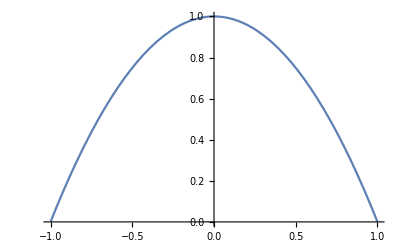

```mathematica
Plot[s[[2]],{xi,-1,1}]
```

```mathematica
s
```

{1+(-1+xi/2) (1+xi),(1-xi) (1+xi),1/2 xi (1+xi)}

```mathematica
f[x]
```

-100 Sin[(π x)/16]

```mathematica
Integrate[ s[[2]],{xi,0,4.}]
```

-17.3333

```mathematica
Integrate[f[xi]s[[1]],{xi,0,4.}]
Integrate[ f[xi] s[[2]],{xi,0,4.}]
Integrate[ f[xi] s[[3]],{xi,0,4.}]
Integrate[ f[xi] s[[1]],{xi,4,8.}]
Integrate[ f[xi] s[[2]],{xi,4,8.}]
Integrate[ f[xi] s[[3]],{xi,4,8.}]
```

-389.437

1023.31

-783.04

-5854.

13548.1

-8054.22

```mathematica
Integrate[f[xi]s[[1]],{xi,0,4}]+Integrate[ f[xi] s[[2]],{xi,0,4}]+Integrate[f[xi] s[[3]],{xi,0,4}]+Integrate[f[xi] s[[1]],{xi,4,8}]+Integrate[f[xi] s[[2]],{xi,4,8}]+Integrate[f[xi] s[[3]],{xi,4,8.}]
```

-509.296

```mathematica
shapes=ComputeShape[2,xi];
newco={0,2,4};
xx=Sum[shapes[[i]] newco[[i]],{i,1,order+1}]
J=D[xx,xi]
vecPtosPesos=GaussianQuadratureWeights[4 order,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((f[xx]shapes[[j]] J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}]
```

2 (1-xi) (1+xi)+2 xi (1+xi)

2 (1-xi)+2 xi

{-0.526566,-100.484,-48.1589}

```mathematica
{-0.5265655570501215,-100.48383547281979,-48.158890401352735}
{-48.903566553611554,-242.58943839774827,-68.63352151148261}
```

{-0.526566,-100.484,-48.1589}

{-48.9036,-242.589,-68.6335}

```mathematica
-0.52-100-48-48-242-68
```

-506.52

```mathematica
shapes=ComputeShape[2,xi];
newco={4,6,8};
xx=Sum[shapes[[i]] newco[[i]],{i,1,order+1}]
J=D[xx,xi]
vecPtosPesos=GaussianQuadratureWeights[4 order,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((f[xx]shapes[[j]] J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}]
```

6 (1-xi) (1+xi)+4 xi (1+xi)+4 (1+(-1+xi/2) (1+xi))

6 (1-xi)+4 xi-2 (1+xi)+4 (-1+xi/2+(1+xi)/2)

{-48.9036,-242.589,-68.6335}

```mathematica
-50-98-170-190
```

-508

```mathematica
SortBy[{3,1,2},Small]
```

{1,2,3}